t^3/ⅇ-t^5/(6 ⅇ)+O[t]^6

t^3/ⅇ-t^5/(6 ⅇ)

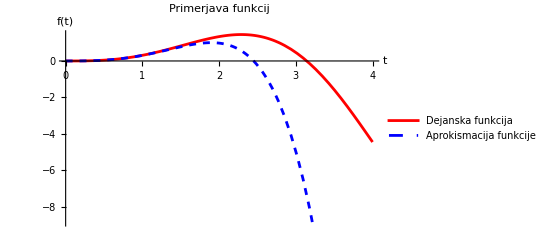

```mathematica
f[t_]:=Sin[t]*t^2*Exp[-1]

taylor=Series[f[t],{t,0,5}]
aproksimacija=Normal[taylor]

Plot[Evaluate[{f[t],aproksimacija}],{t,0,4},PlotStyle->{Directive[Red,Thick],Directive[Blue,Dashed]},PlotLegends->{"Dejanska funkcija","Aprokismacija funkcije"},AxesLabel->{"t","f(t)"},PlotLabel->"Primerjava funkcij"]
```